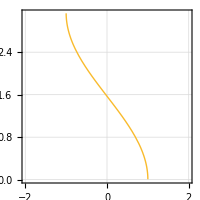

```mathematica
Plot[ArcCos[x],{x,-2,2}]
```

```mathematica
bsq[Jz_]:=1/π ArcCos[-Jz]
K[bsq_]:=1/(2bsq)
u[bsq_]:=1/(1-bsq)*Sin[π(1-bsq)] 1/2
```

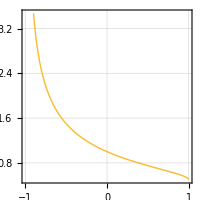

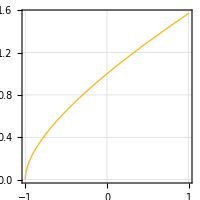

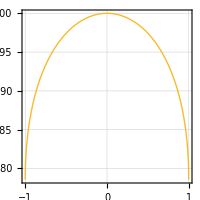

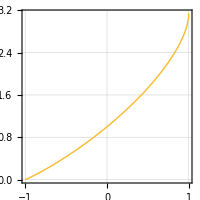

```mathematica
Plot[K[bsq[Jz]],{Jz,-1,1}]
Plot[u[bsq[Jz]],{Jz,-1,1}]
Plot[u[bsq[Jz]]*K[bsq[Jz]],{Jz,-1,1}]
Plot[u[bsq[Jz]]/K[bsq[Jz]],{Jz,-1,1}]
```

```mathematica
Series[K[bsq[J]],{J,0,2}]
```

1-(2 J)/π+(4 J^2)/π^2+O[J]^3

```mathematica
Series[u[bsq[J]],{J,0,2}]
```

1+(2 J)/π+1/2 (-1+8/π^2) J^2+O[J]^3

```mathematica
Series[u[bsq[J]]*K[bsq[J]],{J,0,2}]//Simplify
```

1+(-1/2+4/π^2) J^2+O[J]^3

```mathematica
Series[u[bsq[J]]/K[bsq[J]],{J,0,2}]//Simplify
```

1+(4 J)/π+(-1/2+8/π^2) J^2+O[J]^3